```mathematica
Clear[theta]
```

```mathematica
theta=θ;
```

```mathematica
Clear[gam,gamU4,gamU1,gamU2,gamU3,S,eta,e]
```

Dirac Matrices in Wyle representation

```mathematica
gamU4={{0,0,1,0},{0,0,0,1},{1,0,0,0},{0,1,0,0}};
```

```mathematica
gamU1={{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}};
```

```mathematica
gamU2={{0,0,0,-I},{0,0,I,0},{0,I,0,0},{-I,0,0,0}};
```

```mathematica
gamU3={{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}};
```

```mathematica
gam[i_]:=gam[i]=KroneckerDelta[i,4]*gamU4+KroneckerDelta[i,1]*gamU1+KroneckerDelta[i,2]*gamU2+KroneckerDelta[i,3]*gamU3;
```

generator of the Lorentz group:
========================

```mathematica
S[m_,n_]:=S[m,n]=1/4*(gam[m].gam[n]-gam[n].gam[m]);
```

metric tensor:
==========

```mathematica
eta={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}};
```

find the rotation matrix in x-z plane:
=========================

```mathematica
Clear[omega,R]
```

```mathematica
omega[i_,j_]:=omega[i,j]=(KroneckerDelta[i,1]*KroneckerDelta[j,3]-KroneckerDelta[j,1]*KroneckerDelta[i,3])*theta
```

```mathematica
M=1/2*∑_(m=1)^4 ∑_(n=1)^4 S[m,n]*omega[m,n]
```

{{0,θ/2,0,0},{-θ/2,0,0,0},{0,0,0,θ/2},{0,0,-θ/2,0}}

```mathematica
R=IdentityMatrix[4]+M+1/2*M.M+1/6*M.M.M+1/24*M.M.M.M
```

{{1-θ^2/8+θ^4/384,θ/2-θ^3/48,0,0},{-θ/2+θ^3/48,1-θ^2/8+θ^4/384,0,0},{0,0,1-θ^2/8+θ^4/384,θ/2-θ^3/48},{0,0,-θ/2+θ^3/48,1-θ^2/8+θ^4/384}}

```mathematica
Series[Cos[theta/2],{theta,0,4}]
```

1-θ^2/8+θ^4/384+O[θ]^5

```mathematica
Series[Sin[theta/2],{theta,0,4}]
```

θ/2-θ^3/48+O[θ]^5

```mathematica
Clear[R]
```

```mathematica
R[theta_]:=R[theta]={{Cos[theta/2],Sin[theta/2],0,0},{-Sin[theta/2],Cos[theta/2],0,0},{0,0,Cos[theta/2],Sin[theta/2]},{0,0,-Sin[theta/2],Cos[theta/2]}}
```

```mathematica
R[theta]
```

{{Cos[θ/2],Sin[θ/2],0,0},{-Sin[θ/2],Cos[θ/2],0,0},{0,0,Cos[θ/2],Sin[θ/2]},{0,0,-Sin[θ/2],Cos[θ/2]}}

Difine the spinors:
==============

```mathematica
Clear[u01,u1,u02,u2,v01,v1,v02,v2,us,vs]
```

```mathematica
u01[p_]:=u01[p]={0,0,√2 √p,0}
```

```mathematica
u1[p_,theta_]:=u1[p,theta]=R[theta].u01[p]
```

```mathematica
u02[p_]:=u02[p]={0,√2 √p,0,0}
```

```mathematica
u2[p_,theta_]:=u2[p,theta]=R[theta].u02[p]
```

```mathematica
v01[p_]:=v01[p]={√2 √p,0,0,0}
```

```mathematica
v1[p_,theta_]:=v1[p,theta]=R[theta].v01[p]
```

```mathematica
v02[p_]:=v02[p]={0,0,0,-√2 √p}
```

```mathematica
v2[p_,theta_]:=v2[p,theta]=R[theta].v02[p]
```

```mathematica
us[p_,theta_,s_]:=us[p,theta,s]=KroneckerDelta[1,s]*u1[p,theta]+KroneckerDelta[2,s]*u2[p,theta]
```

```mathematica
vs[p_,theta_,s_]:=vs[p,theta,s]=KroneckerDelta[1,s]*v1[p,theta]+KroneckerDelta[2,s]*v2[p,theta]
```

some print out. Ignore them
=====================

```mathematica
us[p,theta,1]
```

{0,0,√2 √p Cos[θ/2],-√2 √p Sin[θ/2]}

```mathematica
us[p,theta,2]
```

{√2 √p Sin[θ/2],√2 √p Cos[θ/2],0,0}

```mathematica
vs[p,theta,1]
```

{√2 √p Cos[θ/2],-√2 √p Sin[θ/2],0,0}

```mathematica
vs[p,theta,2]
```

{0,0,-√2 √p Sin[θ/2],-√2 √p Cos[θ/2]}

```mathematica
MatrixForm[S[1,2]]
```

(-ⅈ/2 | 0 | 0 | 0
0 | ⅈ/2 | 0 | 0
0 | 0 | -ⅈ/2 | 0
0 | 0 | 0 | ⅈ/2)

```mathematica
MatrixForm[S[4,2]]
```

(0 | ⅈ/2 | 0 | 0
-ⅈ/2 | 0 | 0 | 0
0 | 0 | 0 | -ⅈ/2
0 | 0 | ⅈ/2 | 0)

```mathematica
gam[4]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
gam[3]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0)

QED propagator:
=============

```mathematica
Clear[propagQED]
```

```mathematica
propagQED[mu_,nu_,q_]:=propagQED[mu,nu,q]=-eta[[mu,nu]]/q
```

```mathematica
TableForm[DeleteCases[Flatten[Table[If[UnsameQ[propagQED[mu1,nu1,q],0],{ToString[ProQED[mu1,nu1,q]]->propagQED[mu1,nu1,q]}],{mu1,1,4},{nu1,1,4}],1],Null]]
```

ProQED[1, 1, q]→-1/q
ProQED[2, 2, q]→-1/q
ProQED[3, 3, q]→-1/q
ProQED[4, 4, q]→1/q

LGT propagator:
============

```mathematica
Clear[propagLGT]
```

```mathematica
propagLGT[mu_,m_,n_,nu_,i_,j_,q_]:=propagLGT[mu,m,n,nu,i,j,q]=-1/2*eta[[mu,nu]]*(eta[[m,i]]*eta[[n,j]]-eta[[m,j]]*eta[[n,i]])/q
```

```mathematica
TableForm[DeleteCases[Flatten[Table[If[UnsameQ[propagLGT[mu,m,n,nu,i,j,q],0],{ToString[Pro[mu,m,n,nu,i,j,q]]->propagLGT[mu,m,n,nu,i,j,q]}],{mu,1,4},{nu,1,4},{m,1,4},{i,1,4},{n,1,4},{j,1,4}],5],Null]];
```

Amplitudes of QED and LGT:
======================

```mathematica
Clear[AmplitudeLGT,AmplitudeQED]
```

```mathematica
AmplitudeQED[s_,r_,sp_,rp_]:=AmplitudeQED[s,r,sp,rp]=∑_(nu=1)^4 (∑_(mu=1)^4 I*e*us[p,theta,sp].gam[4].gam[mu].vs[p,theta,rp]*propagQED[mu,nu,ss])*I*e*vs[p,0,r].gam[4].gam[nu].us[p,0,s]-∑_(nu=1)^4 (∑_(mu=1)^4 I*e*us[p,theta,sp].gam[4].gam[mu].us[p,0,s]*propagQED[mu,nu,tt])*I*e*vs[p,0,r].gam[4].gam[nu].vs[p,theta,rp]
```

```mathematica
TableForm[DeleteCases[Flatten[Table[If[UnsameQ[AmplitudeQED[s,r,sp,rp],0],{ToString[AmpliQED[s,r,sp,rp]]->AmplitudeQED[s,r,sp,rp]}],{sp,1,2},{s,1,2},{rp,1,2},{r,1,2}],3],Null]]/.{ss->4p^2,tt->2p^2(1-Cos[theta])}//Simplify
```

AmpliQED[1, 1, 1, 1]→2 e^2 Csc[θ/2]^2
AmpliQED[1, 2, 1, 2]→-e^2 (-3+Cos[θ]) Cot[θ/2]^2
AmpliQED[2, 1, 1, 2]→-2 e^2 Sin[θ/2]^2
AmpliQED[1, 2, 2, 1]→-2 e^2 Sin[θ/2]^2
AmpliQED[2, 1, 2, 1]→-e^2 (-3+Cos[θ]) Cot[θ/2]^2
AmpliQED[2, 2, 2, 2]→2 e^2 Csc[θ/2]^2

```mathematica
AmplitudeLGT[s_,r_,sp_,rp_]:=AmplitudeLGT[s,r,sp,rp]=∑_(nu=1)^4 ∑_(i=1)^4 ∑_(j=1)^4 (∑_(mu=1)^4 ∑_(m=1)^4 ∑_(n=1)^4 g*us[p,theta,sp].gam[4].gam[mu].S[m,n].vs[p,theta,rp]*propagLGT[mu,m,n,nu,i,j,ss])*g*vs[p,0,r].gam[4].gam[nu].S[i,j].us[p,0,s]-∑_(nu=1)^4 ∑_(i=1)^4 ∑_(j=1)^4 (∑_(mu=1)^4 ∑_(m=1)^4 ∑_(n=1)^4 g*us[p,theta,sp].gam[4].gam[mu].S[m,n].us[p,0,s]*propagLGT[mu,m,n,nu,i,j,tt])*g*vs[p,0,r].gam[4].gam[nu].S[i,j].vs[p,theta,rp]
```

```mathematica
TableForm[DeleteCases[Flatten[Table[If[UnsameQ[AmplitudeLGT[s,r,sp,rp],0],{ToString[Ampli[s,r,sp,rp]]->AmplitudeLGT[s,r,sp,rp]}],{sp,1,2},{s,1,2},{rp,1,2},{r,1,2}],3],Null]]/.{ss->-4p^2,tt->2p^2(1-Cos[theta])}//Simplify
```

Ampli[1, 2, 1, 2]→-3/8 g^2 Csc[θ/2]^6 Sin[θ]^4
Ampli[2, 1, 1, 2]→0
Ampli[1, 2, 2, 1]→0
Ampli[2, 1, 2, 1]→-3/8 g^2 Csc[θ/2]^6 Sin[θ]^4

Add the amplitudes and find the total one:
================================

```mathematica
Clear[Amplitude,e,g]
```

```mathematica
Amplitude[s_,r_,sp_,rp_]:=Amplitude[s,r,sp,rp]=AmplitudeLGT[s,r,sp,rp]+AmplitudeQED[s,r,sp,rp]
```

Amplitude Squre:
=============

```mathematica
Clear[AmpSq]
```

```mathematica
AmpSq[s_,r_,sp_,rp_]:=AmpSq[s,r,sp,rp]=Refine[Simplify[Amplitude[s,r,sp,rp]*Conjugate[Amplitude[s,r,sp,rp]]],Element[{a,b,ss,tt,p,e,g,theta},Reals]]
```

```mathematica
TableForm[DeleteCases[Flatten[Table[If[UnsameQ[AmpSq[s,r,sp,rp],0],{ToString[M2[s,r,sp,rp]]->Simplify[AmpSq[s,r,sp,rp]]}],{sp,1,2},{s,1,2},{rp,1,2},{r,1,2}],3],Null]]/.{ss->-4p^2,tt->2p^2(1-Cos[theta])}//FullSimplify
```

M2[1, 1, 1, 1]→4 e^4 Csc[θ/2]^4
M2[1, 2, 1, 2]→4 (e^2-3 g^2)^2 Cos[θ/2]^4 Cot[θ/2]^4
M2[2, 1, 1, 2]→4 e^4 Sin[θ/2]^4
M2[1, 2, 2, 1]→4 e^4 Sin[θ/2]^4
M2[2, 1, 2, 1]→4 (e^2-3 g^2)^2 Cos[θ/2]^4 Cot[θ/2]^4
M2[2, 2, 2, 2]→4 e^4 Csc[θ/2]^4

Sum over spins of M^2:
===================

```mathematica
Clear[MSquareSpinSum]
```

```mathematica
MSquareSpinSum=Normal[∑_(sp=1)^2 ∑_(s=1)^2 ∑_(rp=1)^2 ∑_(r=1)^2 Series[1/4*AmpSq[s,r,sp,rp],{e,0,4}]/.{ss->-4p^2,tt->2p^2(1-Cos[theta])}//FullSimplify]
```

(e^4 (7+Cos[2 θ])^2)/(4 (-1+Cos[θ])^2)+18 g^4 Cos[θ/2]^4 Cot[θ/2]^4-3/64 e^2 g^2 Csc[θ/2]^12 Sin[θ]^8

To make sure the first term is realy the QED cross section:
==========================================

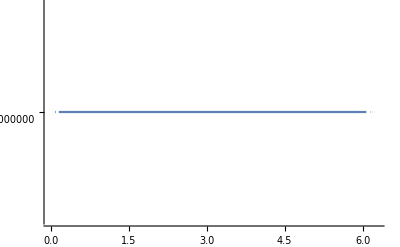

```mathematica
Plot[(7+Cos[2 theta])^2/(4 (-1+Cos[theta])^2)/((1+Cos[theta/2]^4)/(Sin[theta/2]^4)+(1+Cos[theta]^2)/2-(2Cos[theta/2]^4)/(Sin[theta/2]^2)),{theta,0,2Pi}]
```